Supplementary material - Host-microbiome feedbacks underlie regime shifts in the gut
John Guittar, Thomas Koffel, Ashley Shade, Christopher A. Klausmeier, Elena Litchman
6/3/2019

## General tools and graphical options

```mathematica
(*setting working directory to the current one*)
SetDirectory[NotebookDirectory[]];

(*setting various graphical options that wil be used throughout the code:
figure size, colors, curve thickness, font size, figure aspect ratio, panels and axis labels, etc*)
szimg=400;

colS=Darker[Green];
colP=Lighter[Red];

thick1=0.004;
thick1b=0.006;
thick2=0.008;

dash=.006;
dash2=.03;
ptsize=0.03;

ftszlbl=18;
ftszplot=18;
AR=.8;
arl=1/6;
szlbl=25;
cdlblb=380;
labl={"A","B","C","D"};
lbl1={"A","B","C","D"};
toplab={"no cross-feeding","low synthesis rates", "high synthesis rates"};

labl={Row[{Style["Carbohydrate concentration (",FontSize->ftszlbl],Style["C",FontSlant->Italic, FontSize->ftszlbl],Style[")",FontSize->ftszlbl]}], Row[{Style["Electron acceptor concentration (",FontSize->ftszlbl],Style["O",FontSlant->Italic, FontSize->ftszlbl],Style[")",FontSize->ftszlbl]}]};

labl2={Row[{Style["Mutualist abundance ",FontSize->ftszlbl],Style[Row[{"(","M",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Pathogen abundance ",FontSize->ftszlbl],Style[Row[{"(","P",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}]};

labl3={Row[{Style["Electron acceptor influx (",FontSize->ftszlbl],Style[Subscript[Style["O",FontSlant->Italic], "in"], FontSize->ftszlbl],Style[")",FontSize->ftszlbl]}], Row[{Style["Electron acceptor concentration (",FontSize->ftszlbl],Style["O", FontSlant->Italic,FontSize->ftszlbl],Style[")",FontSize->ftszlbl]}]};
```

```mathematica
(*Graphical function to rasterize RegionPlots when exporting them in PDF*)
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

(*Defining various general tools for drawing species niches*)
(*General function to draw the Zero Net Growth Isocline (ZNGI) of the species given in input*)
PlotZNGI[{R_,Z_,γ_,u_,tmin_,tmax_,Col_},thick_,labl_]:=ParametricPlot[If[R[t]<Rmax&&Z[t]<Zmax,{R[t],Z[t]}],{t,tmin,tmax},PlotStyle->{Col,Thickness[thick]},AspectRatio->AR,PlotRange->{{Rmin,Rmax},{Zmin,Zmax}},FrameLabel ->labl];

(*General function to draw the impact vector of the species given in input*)
PlotIR[{R_,Z_,{γ1_,γ2_},u_,tmin_,tmax_,Col_},t_,thick_,dashing_,s_]:= Show[Graphics[{Col, Thickness[thick],If[dashing==1,{},Dashing[dashing]],Line[{{s[[1]],s[[2]]},{R[t],Z[t]}}]}],Graphics[{Col,PointSize[ptsize],Point[{R[t],Z[t]}]}]];

(*General function to draw the impact maps for a given supply point. If alternative stable states, draws both maps*)
IVmap[{Ci_,O2i_}]:=Module[{eq,OeqS,eqS,OeqP,eqP,Cin,da},
ClearCache[gS,gP,eq,limP,dgS,dgP];
O2in=O2i;
Cin=Ci;
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2i,Cb->Ci},10^6,Fixed->{S->Sv,P->Pv}]];
If[(GivesolS[Ci,O2i]=={})||(GivesolP[Ci,O2i]=={}),da=1,da=dash];
Show [If[GivesolS[Ci,O2i]=={},{},eqS=GivesolS[Ci,O2i][[1,1;;2]];OeqS=O2/.eq[eqS[[1]],eqS[[2]]];PlotIR[spS,OeqS,thick1b,da,{Ci,O2i}]],If[GivesolP[Ci,O2i]=={},{},eqP=GivesolP[Ci,O2i][[1,1;;2]];OeqP=O2/.eq[eqP[[1]],eqP[[2]]];PlotIR[spP,OeqP,thick1b,da,{Ci,O2i}]],
{Graphics[ {PointSize[ptsize],Point[{Ci,O2i}]}],Graphics[ {White,PointSize[ptsize/1.5],Point[{Ci,O2i}]}]}]]

(*General functions to draw the persistence niche of the species given in input*)
PlotPersist[{R_,Z_,{γ1_,γ2_},u_,tmin_,tmax_,Col_},labl_]:=RegionPlot[u[RR,ZZ]>0||((RR-R[tmin])*γ2[tmin]>(ZZ-Z[tmin])*γ1[tmin])&&RR>R[tmin],{RR,Rmin,Rmax+1},{ZZ,Zmin-1,Zmax+1},PlotRange->{{Rmin,Rmax},{Zmin,Zmax}},PlotStyle->{Lighter[Lighter[Col]],Opacity[0.4]},BoundaryStyle->{Col,Opacity[1.0],Thickness[thick2],Dashing[dash2]},FrameLabel -> labl,PlotPoints->50,MaxRecursion->5,AspectRatio->AR];
(*General functions to draw the realized persistence niche of the first species given in input, when the second species in input is present*)
PlotPersist2[{R_,Z_,{γ1_,γ2_},u_,tmin_,tmax_,Col_},{R2_,Z2_,γ2b_,u2_,tmin2_,tmax2_,Col2_},labl_]:=RegionPlot[(u[RR,ZZ]>0&&u2[RR,ZZ]<0)||((RR-R[tmin])*γ2[tmin]<(ZZ-Z[tmin])*γ1[tmin])&&RR>R[tmin],{RR,Rmin,Rmax+1},{ZZ,Zmin-1,Zmax+1},PlotRange->{{Rmin,Rmax},{Zmin,Zmax}},PlotStyle->{Lighter[Lighter[Col]],Opacity[0.4]},BoundaryStyle->{Col,Opacity[1.0],Thickness[thick2],Dashing[dash2]},FrameLabel -> labl,PlotPoints->50,MaxRecursion->5,AspectRatio->AR];


(*Defining various general tools for drawing phase planes and streamplots*)
(*Tool to draw the equilibrium points in the phase plane*)
PtPoint[pt_,st_]:=Show[Graphics[ {PointSize[0.03],If[Chop[pt[[1]]]==0&&Chop[pt[[2]]]≠0,colP,If[Chop[pt[[1]]]≠0&&Chop[pt[[2]]]==0,colS,Black]],Point[pt]}],Graphics[ {PointSize[0.02],If[st==1,Black,White],Point[pt]}]];

(*Tool to draw a trajectory starting form the initial conditions (S0,P0) in the phase plane*)
PlotTraj[S0_,P0_,tmax_,plotstyle_]:=Module[{eqs,sol,Ssol,Psol},
eqs={S'[t]==dgS[S[t],P[t]],P'[t]==dgP[S[t],P[t]],S[0]==S0,P[0]==P0};
sol=NDSolveValue[eqs,{S,P},{t,0,tmax}];
Ssol[t_]:=sol[[1]][t];
Psol[t_]:=sol[[2]][t];
ParametricPlot[{Ssol[t],Psol[t]},{t,0,tmax},PlotRange->All,PlotStyle->plotstyle]]

(*Tool to draw the separatrix between basin of attractions in the phase plane*)
PlotBassin[Cin_,O2in_,tmax_,side_]:=Module[{eqs,sol,Ssol,Psol},
{S0,P0}=Bcx[Cin,O2in]+side*{.01,.01};
eqs={S'[t]==-dgS[S[t],P[t]],P'[t]==-dgP[S[t],P[t]],S[0]==S0,P[0]==P0};
sol=NDSolveValue[eqs,{S,P},{t,0,tmax}];
Ssol[t_]:=sol[[1]][t];
Psol[t_]:=sol[[2]][t];
ParametricPlot[{Ssol[t],Psol[t]},{t,0,tmax},PlotRange->All,PlotStyle->{Gray,Thickness[thick1b]}]]
```

## Setting the Model and derived tools

```mathematica
(*Setting the Ecological model using the EcoEvo package by C. A. Klausmeier*)
(*listing the variables*)

(*/!| note that the Mutualist variable is here denoted "S" and not "M"          /!|*)
(*/!| note that the electron acceptor variable is here denoted "O2" and not "O" /!|*)
(*/!| note that the carbon substrate variable is here denoted "Cb" and not "C"  /!|*)
SetModel[{
Aux[1]->{Variable->O2,Equation:>dO},
Aux[2]->{Variable->Cb,Equation:>dC},
Pop[1]->{Variable->S,Equation:>dS},
Pop[2]->{Variable->P,Equation:>dP}
}]

(*specifying the dynamics*)
dO:=aO(O2in-O2[t])-qOP*μP*P[t]+γOP/(hOP+O2[t])*P[t]-qOE*αE*O2[t]*Ecell/(aG+qBE*αE*O2[t]*Ecell)*(γBS*S[t]);
dC:=aG(Cin-Cb[t])-qCP*μP*P[t]-qCS*Min[μSx,μCS]*S[t];
dS:=(μS-mS)S[t];
dP:=(μP-mP)P[t];

(*specifying the growth functions*)
μS:=Min[μSx,μCS]-βS*O2[t];
μCS:=αCS*Cb[t];
μP:=Min[μPx,αCP*Cb[t],αOP*O2[t]];
```

```mathematica
(*specifying all the numerical values for the different parameters*)
αCS=1;
βS=1;
μSx=2;
mS=1/2;

αCP=1;
αOP=1;
μPx=2;
mP=1;

aG=1;
qCS=1;
qCP=1;

aG=1;
γBS=3;
αE=1;
qBE=1;
qOP=1;

aO=1;
γOP=2.4;
hOP=1;
qOE=1;

Ecell=.16;

(*A few derived parameters*)
OminP=mP/αOP; (*R^* of the Pathogen for oxygen when carbon is not limiting*)
CminP=mP/αCP; (*R^* of the Pathogen for carbon when oxygen is not limiting*)
OmaxS=(μSx-mS)/βS//N; (*Maximal value of oxygen the Mutualist can tolerate when carbon is not limiting --- this is equivalent to the "P^*" of a species in Holt's apparent competition framework*)

(*This are the coordinates of the intersection between the Pathogen and the Mutualist isoclines*)
{Ocx,Ccx}={OminP,(βS*OminP+mS)/αCS};
(*This are the densities of the two species at the coexistence equilibrium. Note that this equilibrium is never stable in this study (no coexistence possible)! *)
Bcx[Cin_,O2in_]:=-Inverse[{{ISC[Ccx,Ocx],IPC[Ccx,Ocx]},{ISO[Ccx,Ocx],IPO[Ccx,Ocx]}}].{aG*(Cin-Ccx),aO*(O2in-Ocx)}

(*these are the boundaries of the window for the niche plots in the carbon substrate - electron acceptor plane*)
Rmin=0;
Cmax=5;
Rmax=Cmax;

Zmin=0;
Omax=1.6;Zmax=Omax;
```

### Formating the two species to draw their niches using the general tools

```mathematica
(*growth rate of the mutualist as a function of carbon substrate and electron acceptor concentrations*)
gSp[Cb_,O2_]:=Evaluate[(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}]
(*impact of the mutualist on the carbon substrate*)
ISC[Cb_,O2_]:=Evaluate[-(qCS*Min[μSx,μCS])/.{O2[t]->O2,Cb[t]->Cb}]
(*impact of the mutualist on the electron acceptor*)
ISO[Cb_,O2_]:=Evaluate[-(qOE*αE*O2[t]*Ecell*γBS/(aG+qBE*αE*O2[t]*Ecell))/.{O2[t]->O2,Cb[t]->Cb}]

(*growth rate of the pathogen as a function of carbon substrate and electron acceptor concentrations*)
gPp[Cb_,O2_]:=Evaluate[(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}]
(*impact of the pathogen on the carbon substrate*)
IPC[Cb_,O2_]:=Evaluate[-(qCP*μP)/.{O2[t]->O2,Cb[t]->Cb}]
(*impact of the pathogen on the electron acceptor*)
IPO[Cb_,O2_]:=Evaluate[-(qOP*μP-γOP/(hOP+O2[t]))/.{O2[t]->O2,Cb[t]->Cb}]

(*equation of the ZNGI of the mutualist*)
CfOS[O2_]:=(βS*O2+mS)/αCS

(*equation of the ZNGI of the pathogen, as C as a function of O.
Because it is not technically possible for the pathogen (completely vertical ZNGI), a trick is used to add a very abrupt slope*)
sc=0.001;
CfOP[O2_]:=CminP+sc*(O2-OminP)

(*all the info necessary to draw the ZNGI and impact vectors of the pathogen and mutualists are gathered in the following lists, as parametric plots of # that run along the ZNGI*)
spS={CfOS[#]&,#&,{ISC[CfOS[#],#]&,ISO[CfOS[#],#]&},gSp[#1,#2]&,OmaxS,0,colS};
spP={CfOP[#]&,#&,{IPC[CfOP[#],#]&,IPO[CfOP[#],#]&},gPp[#1,#2]&,OminP,Omax,colP};

(*In the presence of the Pathogen, the realized niche of the Mutualist is reduced (due to competition), leading to a new boundary of the ZNGI (OmaxSu instead of OmaxS)*)
If[OminP<OmaxS,OmaxSu=OminP];
spSu={CfOS[#]&,#&,{ISC[CfOS[#],#]&,ISO[CfOS[#],#]&},gSp[#1,#2]&,OmaxSu,0,Darker[Green]};
```

### Extra-tools for bifurcation diagrams

```mathematica
(*Solve for the abundance of the Pathogen at equilibrium when the Mutualist is excluded, for a given supply point*)
GivesolP[Cin_,O2in_]:=Module[{solP,solbP,ret},
solP=Quiet[Solve[{(Min[μPx,αCP*Cb,αOP*O2]-mP)==0,aO(O2in-O2)-qOP*Min[μPx,αCP*Cb,αOP*O2]*P+γOP/(hOP+O2)*P==0,aG(Cin-Cb)-qCP*Min[μPx,αCP*Cb,αOP*O2]*P==0},{Cb,O2,P}]];
If[solP=={},ret={},
solbP={Cb,O2,P}/.solP;
If[solbP[[2,3]]>0,ret={{0,solbP[[1,3]],1},{0,solbP[[2,3]],0}},ret={{0,solbP[[1,3]],1}}]
];
ret]
(*Solve for the oxygen concentration at equilibrium when the Mutualist is excluded, for a given supply point*)
GivesolPO[Cin_,O2in_]:=Module[{solP,solbP,ret},
solP=Quiet[Solve[{(Min[μPx,αCP*Cb,αOP*O2]-mP)==0,aO(O2in-O2)-qOP*Min[μPx,αCP*Cb,αOP*O2]*P+γOP/(hOP+O2)*P==0,aG(Cin-Cb)-qCP*Min[μPx,αCP*Cb,αOP*O2]*P==0},{Cb,O2,P}]];
If[solP=={},ret={},
solbP={Cb,O2,P}/.solP;
ret=solbP[[1,2]]
];
ret]

(*Solve for the abundance of the Mutualist  at equilibrium when the Pathogen is excluded, for a given supply point*)
GivesolS[Cin_,O2in_]:=Module[{solS,solbS,ret},
solS=Quiet[Solve[{(Min[μSx,αCS*Cb]-βS*O2-mS)==0,aO(O2in-O2)-qOE*αE*O2*Ecell/(aG+qBE*αE*O2*Ecell)*(γBS*S)==0,aG(Cin-Cb)-qCS*Min[μSx,αCS*Cb]*S==0},{Cb,O2,S}]];
If[solS=={},ret={},
solbS={Cb,O2,S}/.solS;
If[solbS[[2,3]]>0,ret={{solbS[[1,3]],0,If[solbS[[1,2]]>OminP,0,1]},{solbS[[2,3]],0,0}},ret={{solbS[[1,3]],0,1}}]
];
ret]
(*Solve for the oxygen concentration  at equilibrium when the Pathogen is excluded, for a given supply point*)
GivesolSO[Cin_,O2in_]:=Module[{solS,solbS,ret},
solS=Quiet[Solve[{(Min[μSx,αCS*Cb]-βS*O2-mS)==0,aO(O2in-O2)-qOE*αE*O2*Ecell/(aG+qBE*αE*O2*Ecell)*(γBS*S)==0,aG(Cin-Cb)-qCS*Min[μSx,αCS*Cb]*S==0},{Cb,O2,S}]];
If[solS=={},ret={},
solbS={Cb,O2,S}/.solS;
ret=solbS[[1,2]];
If[solbS[[1,2]]>OminP,ret={}];
];
ret]
```

## Figures

### Drawing Figure 3

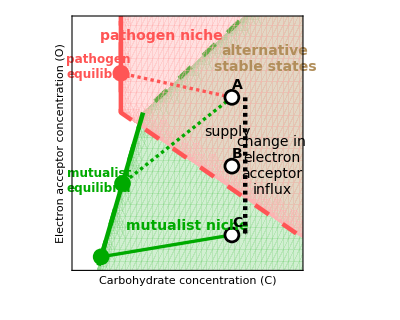

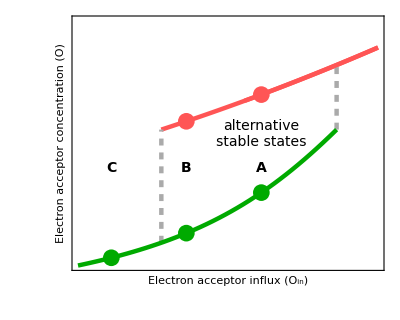

```mathematica
(*defining the coordinates of the three supply points singled out on Fig. 3a-b, and labeling them*)
Cin=3.5;
O2l={1.1,.65,.2};
labpan={"A","B","C"};

(*Fig. 3a*)
(*Graphical options and text*)
text1=Graphics[ {Text[Style["mutualist
equilibria", 12,Bold,colS],{0.5,0.55}]}];
text2=Graphics[ {Text[Style["pathogen
equilibria", 12,Bold,colP],{0.5,1.3}]}];
text3=Graphics[ {Text[Style["change in
electron
acceptor
influx", 14],{4.4,(O2l[[1]]+O2l[[-1]])/2}]}];
text4=Graphics[ {Text[Style["pathogen niche", 14,colP,Bold],{1.9,1.5}]}];
text5=Graphics[ {Text[Style["mutualist niche", 14,colS,Bold],{2.5,.26}]}];
text6=Graphics[ {Text[Style["supply", 14],{3.4,(O2l[[1]]+O2l[[2]])/2}]}];
text7=Graphics[ {Text[Style["alternative
stable states", 14,RGBColor[177/255,142/255,90/255],Bold],{4.25,1.35}]}];
ofC=.3;
dash3=.007;
arrow1=Graphics[{Thickness[thick2],Dashing[dash3],Arrow[{{Cin+ofC,O2l[[1]]},{Cin+ofC,O2l[[-1]]}}]}];

(*Using the general niche toolbox to plot the persistence niches, ZNGIs and impact vector map of the two species*)
fig5a=Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Table[IVmap[{Cin,O2l[[i]]}],{i,{1,3}}],text1,text2,text3,text4,text5,text6,text7,arrow1,
Table[Graphics[{ Text[Style[labpan[[i]], 14,Bold,Black],{Cmax/40,Omax/20}+{Cin,O2l[[i]]}]}],{i,Length[O2l]}],
{Graphics[ {PointSize[ptsize],Point[{Cin,O2l[[2]]}]}],Graphics[ {White,PointSize[ptsize/1.5],Point[{Cin,O2l[[2]]}]}]},
FrameTicks->False]

(*Fig. 3b*)
(*Computing the coordinates of the two hysteresis*)
OminP2=OminP;
O2inup=O2i/.Quiet[Solve[{(Min[μSx,αCS*Cb]-βS*OminP2-mS)==0,aO(O2i-OminP2)-qOE*αE*OminP2*Ecell/(aG+qBE*αE*OminP2*Ecell)*(γBS*S)==0,aG(Cin-Cb)-qCS*Min[μSx,αCS*Cb]*S==0},{Cb,O2i,S}]][[1]];
O2indn=O2i/.Quiet[Solve[{(αCP*Cb-mP)==0,aO(O2i-OminP2)-qOP*αCP*Cb*P+γOP/(hOP+OminP2)*P==0,aG(Cin-Cb)-qCP*αCP*Cb*P==0},{Cb,O2i,P}]][[1]];

(*Graphical options*)
labl3b=Flatten[{labl3,Row[{Style[Subscript["C", "in"], FontSize->ftszlbl],Style[" = ",FontSize->ftszlbl],Style[Cin,FontSize->ftszlbl]}]}];
labl3b=labl3;
text1b=Graphics[ {Text[Style["alternative
stable states", 14],{1.1,.97}]}];
Omax2=1.8;

(*Plotting the bifurcation diagram of the equilibrium electron acceptor concentration as a function of its supply: pathogen branch(es), mutualist branch, hysteresis*)
fig5b=Show[Plot[GivesolPO[Cin,Oin],{Oin,0,Omax2},PlotRange->{{0,Omax2},{0,1.8}},PlotStyle->{colP,Thickness->thick2}],Table[Graphics[{Thickness->thick2,Dashed,Lighter[Gray],Line[{{O2i,GivesolSO[Cin,O2i]},{O2i,GivesolPO[Cin,O2i]}}]}],{O2i,{O2indn,O2inup}}],
Plot[GivesolPO[Cin,Oin],{Oin,OminP,Omax2},PlotRange->{{0,Omax2},{0,All}},PlotStyle->{colP,Thickness->thick2}],
Plot[GivesolSO[Cin,Oin],{Oin,0,Omax2},PlotRange->{{0,Omax2},{0,All}},PlotStyle->{colS,Thickness->thick2}],
Table[If[ToString[GivesolPO[Cin,O2l[[i]]]]=="{}",{},Graphics[ {PointSize[0.03],colP,Point[{O2l[[i]],GivesolPO[Cin,O2l[[i]]]}]}]],{i,Length[O2l]}],
Table[If[ToString[GivesolSO[Cin,O2l[[i]]]]=="{}",{},Graphics[ {PointSize[0.03],colS,Point[{O2l[[i]],GivesolSO[Cin,O2l[[i]]]}]}]],{i,Length[O2l]}],
Table[Graphics[{ Text[Style[labpan[[i]], 14,Bold,Black],{O2l[[i]],Omax2/2.5}]}],{i,Length[O2l]}],
text1b,
Frame->True,FrameLabel->labl3b,AspectRatio->AR,FrameTicks->False]

(*Exporting panels a and b in both PNG and PDF formats*)
Export[StringJoin["figures/fig5a.png"],fig5a,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig5a.pdf"],fig5a,"PDF"];
Export[StringJoin["figures/fig5b.png"],fig5b,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig5b.pdf"],fig5b,"PDF"];
```

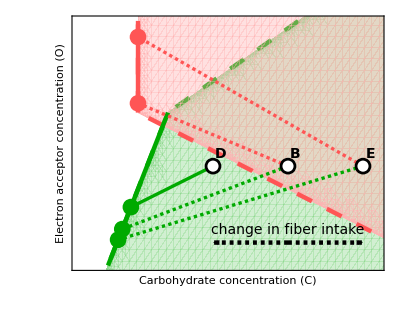

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

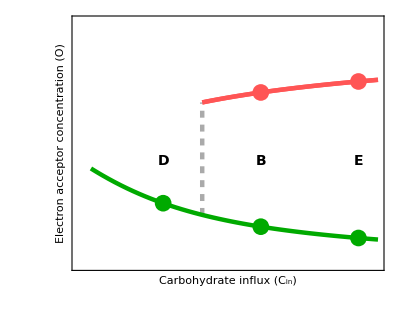

```mathematica
(*defining the coordinates of the three other supply points singled out on Fig. 3c-d, and labeling them. Note that one of the supplies is shared between the two figures*)
O2in=O2l[[2]];
Cl={2.25,Cin,4.75};
labpan2={"D",labpan[[2]],"E"};

(*Fig. 3c*)
(*Graphical options and text*)
ofC=-.55;
ofC=-.5;
dash3=.007;
text1=Graphics[ {Text[Style["change in fiber intake", 14],{(Cl[[1]]+Cl[[3]])/2,O2in+ofC+.08}]}];
arrow1=Graphics[{Thickness[thick2],Dashing[dash3],Arrow[{{Cl[[2]],O2in+ofC},{Cl[[1]],O2in+ofC}}]}];
arrow2=Graphics[{Thickness[thick2],Dashing[dash3],Arrow[{{Cl[[2]],O2in+ofC},{Cl[[3]],O2in+ofC}}]}];

(*Using the general niche toolbox to plot the persistence niches, ZNGIs and impact vector map of the two species*)
fig5c=Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Table[IVmap[{Cl[[i]],O2in}],{i,{1,2,3}}],text1,arrow1,arrow2,
Table[Graphics[{ Text[Style[labpan2[[i]], 14,Bold,Black],{Cmax/40,Omax/20}+{Cl[[i]],O2in}]}],{i,Length[Cl]}],FrameTicks->False]

(*Fig. 3d*)
(*Computing the coordinates of the two hysteresis*)
Cindn=Ci/.Quiet[Solve[{(αCP*Cb-mP)==0,aO(O2in-OminP2)-qOP*αCP*Cb*P+γOP/(hOP+OminP2)*P==0,aG(Ci-Cb)-qCP*αCP*Cb*P==0},{Cb,Ci,P}]][[1]];

(*Graphical options*)
text1=Graphics[ {Text[Style["healthy", 14,Bold,colS],{4,0.4}]}];
text2=Graphics[ {Text[Style["dysbiosis", 14,Bold,colP],{4,1.35}]}];
labl4={Row[{Style["Carbohydrate influx (",FontSize->ftszlbl],Style[Subscript[Style["C",FontSlant->Italic], "in"], FontSize->ftszlbl],Style[")",FontSize->ftszlbl]}], Row[{Style["Electron acceptor concentration (",FontSize->ftszlbl],Style["O",FontSlant->Italic, FontSize->ftszlbl],Style[")",FontSize->ftszlbl]}]};
labl3b=Flatten[{labl4,Row[{Style[Subscript["O", "in"], FontSize->ftszlbl],Style[" = ",FontSize->ftszlbl],Style[O2in,FontSize->ftszlbl]}]}];
labl3b=labl4;
text1b=Graphics[ {Text[Style["alternative
stable states", 14],{4.2,.65}]}];
CminS=(Cb/.Solve[gSp[Cb,O2in]==0,Cb][[1]])+0.01;
Omaxb=1.5;

(*Plotting the bifurcation diagram of the equilibrium carbon concentration as a function of the electron acceptor supply: pathogen branch(es), mutualist branch, hysteresis*)
fig5d=Show[Plot[GivesolPO[Cin,O2in],{Cin,CminS,Cmax},PlotRange->{{CminS,Cmax},{0,Omaxb}},PlotStyle->{colP,Thickness->thick2}],
Table[Graphics[{Thickness->thick2,Dashed,Lighter[Gray],Line[{{Ci,GivesolSO[Ci,O2in]},{Ci,GivesolPO[Ci,O2in]}}]}],{Ci,{Cindn}}],
Plot[GivesolPO[Cin,O2in],{Cin,CminS,Cmax},PlotRange->{{0,Cmax},{0,All}},PlotStyle->{colP,Thickness->thick2}],
Plot[GivesolSO[Cin,O2in],{Cin,CminS,Cmax},PlotRange->{{0,Cmax},{0,All}},PlotStyle->{colS,Thickness->thick2}],
Table[If[ToString[GivesolPO[Cl[[i]],O2in]]=="{}",{},Graphics[ {PointSize[0.03],colP,Point[{Cl[[i]],GivesolPO[Cl[[i]],O2in]}]}]],{i,Length[Cl]}],
Table[If[ToString[GivesolSO[Cl[[i]],O2in]]=="{}",{},Graphics[ {PointSize[0.03],colS,Point[{Cl[[i]],GivesolSO[Cl[[i]],O2in]}]}]],{i,Length[Cl]}],
Table[Graphics[{ Text[Style[labpan2[[i]], 14,Bold,Black],{Cl[[i]],Omax/2.5}]}],{i,Length[Cl]}],
Frame->True,FrameLabel->labl3b,AspectRatio->AR,FrameTicks->False]

(*Exporting panels c and d in both PNG and PDF formats*)
Export[StringJoin["figures/fig5c.png"],fig5c,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig5c.pdf"],fig5c,"PDF"];
Export[StringJoin["figures/fig5d.png"],fig5d,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig5d.pdf"],fig5d,"PDF"];
```

### Drawing Figure 2

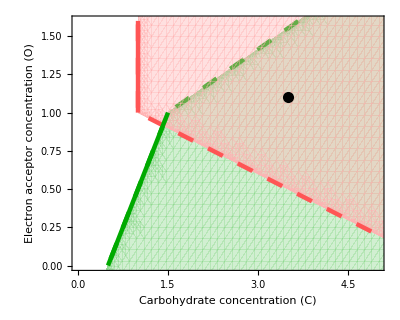

{{0,0},{0.700483,0.949275},{2.37722,0},{0,2.5}}

{0,0,1,1}

```mathematica
(*Selecting the supply point from Figure 2; note that this is "supply point A" from Figure 3*)
O2in=O2l[[1]];
Cin=Cl[[2]];
s={Cin,O2in};

(*Displaying where the supply point is located in the niche space*)
Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Graphics[ {PointSize[0.02],Point[{s[[1]],s[[2]]}]}]]

(*Setting the dynamical equations for the Quasi Steady State Approximation.
The function "eq" uses the EcoSim function from the EcoEvo package to simulate numerically the equilibriation of O2 and C, leading the QSSA values of O2 and Cb as functions of S and P*)
ClearCache[gS,gP,eq,limP,dgS,dgP];
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2in,Cb->Cin},10^6,Fixed->{S->Sv,P->Pv}]];
(*Per capita growth rate of the Mutualists and Pathogens after QSSA on O2 and Cb*)
gS[Sv_?NumericQ,Pv_?NumericQ]:=gS[Sv,Pv]=(μS-mS/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
gP[Sv_?NumericQ,Pv_?NumericQ]:=gP[Sv,Pv]=(μP-mP/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
(*Population growth rates of the Mutualists and Pathogens after QSSA on O2 and Cb*)
dgS[Sv_?NumericQ,Pv_?NumericQ]:=dgS[Sv,Pv]=(Sv*(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgP[Sv_?NumericQ,Pv_?NumericQ]:=dgP[Sv,Pv]=(Pv*(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])

(*Solving for the different equilibrium points for this supply points*)
eqlist=Join[{{0,0}},If[Min[Bcx[Cin,O2in]]<0,{},{Bcx[Cin,O2in]}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,1;;2]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,1;;2]]]]
(*Checking stability of the different equilibrium points for this supply points*)
stablist=Join[If[(Min[μPx,αCP*Cin,αOP*O2in]-mP<0)&&(Min[μSx,αCS*Cin]-βS*O2in-mS<0),1,{0}],If[Min[Bcx[Cin,O2in]]<0,{},{0}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,3]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,3]]]]

(*Getting the coordinates of the Mutualist equilibrium. Used below for the test function*)
ptH=eqlist[[3]];
(*This is a test function that returns the
Allows to color plot the streamplot in red vs green depending on what equlibrium the stream leads to
Note that this function significantly slows down the computation. It can be turned off by replacing it with the dummy test function that is commented below, and always returns true, significantly speeding up the streamplot*)
test[{Sv0_?NumericQ,Pv0_?NumericQ},ptH_]:=Module[{x,y,t,res},res=NDSolveValue[{S'[t]==dgS[S[t],P[t]],P'[t]==dgP[S[t],P[t]],S[0]==Sv0,P[0]==Pv0},{S,P},{t,0,1000}];
Norm[ptH-Through[res[100]]]<.01]
(*test[{Sv0_?NumericQ,Pv0_?NumericQ},ptH_]:=Module[{x,y,t,res},1;True]*)
```

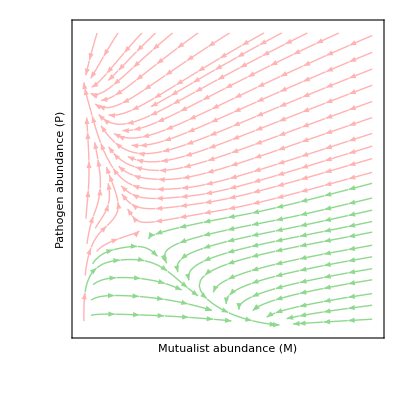

```mathematica
(*panel a*)
(*Setting the graphical window for the streamplot in the phase plane*)
Sx=3.5;
Px=3;

(*plots the streamplot of the 2D dynamical system*)
stream=StreamPlot[{dgS[Sv,Pv],dgP[Sv,Pv]},{Sv,0,Sx},{Pv,0,Px},StreamColorFunction->Function[{Sv,Pv},If[test[{Sv,Pv},ptH],Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,FrameTicks->False,FrameLabel -> labl2]
```

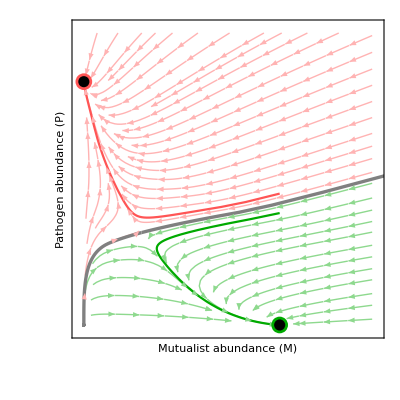

```mathematica
(*Draws the isoclines of the 2D dynamical system (not represented) *)
iso=ContourPlot[{dgS[Sv,Pv]==0,dgP[Sv,Pv]==0(*limP[Sv,Pv]==0,*)},{Sv,0,Sx},{Pv,0,Px},MaxRecursion->5,ContourStyle->{{colS,Thickness[thick2]},{colP,Thickness[thick2]},{colS,Thickness[thick2]},{colP,Thickness[thick2]}},FrameLabel -> labl2,AspectRatio->AR];
fig2=Show[stream,PlotBassin[Cin,O2in,1000,-.01],PlotBassin[Cin,O2in,17.5,.01],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]];

(*adds the separatrix between the basin of attraction*)
fig2b=Show[stream,PlotBassin[Cin,O2in,1000,-.01],PlotBassin[Cin,O2in,17.5,.01]];

(*initial conditions for the two trajectories that have been singled out*)
condini1={eqlist[[3,1]],1.15};
condini2={eqlist[[3,1]],1.35};

(*adds the two trajectories; this is the final figure*)
fig2c=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],10^3,{colP,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]]

(*Export the figure in PNG and PDF*)
Export[StringJoin["figures/fig2a.png"],fig2c,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig2a.pdf"],fig2c,"PDF"];
```

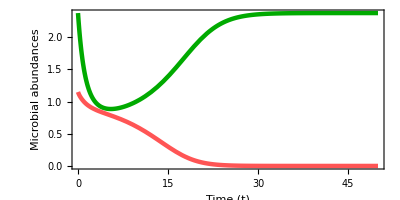

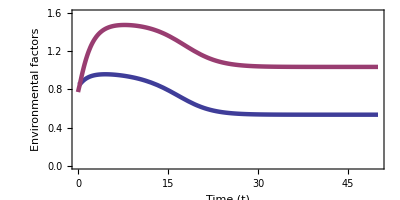

```mathematica
(*Another visualization of the trajectories plotted above, this time as a function of time*)
(*Another tool that computes the trajectories of S, P, O2 and Cb through time when the QSSA is accounted for*)
PlotTrajAbun[S0_,P0_,tmax_,plotstyle_]:=Module[{eqs,sol,Ssol,Psol},
eqs={S'[t]==dgS[S[t],P[t]],P'[t]==dgP[S[t],P[t]],S[0]==S0,P[0]==P0};
sol=NDSolveValue[eqs,{S,P},{t,0,tmax}];
Ssol[t_]:=sol[[1]][t];
Psol[t_]:=sol[[2]][t];
abun=Plot[{Ssol[t],Psol[t]},{t,0,tmax},PlotRange->All,PlotStyle->{{colS,plotstyle},{colP,plotstyle}},Frame->True,FrameLabel -> {Row[{Style["Time ",FontSize->ftszlbl],Style[Row[{"(","t",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Microbial abundances ",FontSize->ftszlbl]}]},AspectRatio->.5];
nut[tt_?NumericQ]:=Evaluate[{O2,Cb}/.eq[Ssol[tt],Psol[tt]]];
envi=Plot[{nut[tt][[1]],nut[tt][[2]]},{tt,0,tmax},PlotRange->{Automatic,{0,1.6}},PlotStyle->{{col1,plotstyle},{col3,plotstyle}},Frame->True,FrameLabel -> {Row[{Style["Time ",FontSize->ftszlbl],Style[Row[{"(","t",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Environmental factors ",FontSize->ftszlbl]}]},AspectRatio->.5];
{abun,envi}]

(*trajectory that ends up at the healthy state (green in previous figure)*)
(*Plotting how the abundance of the Mutualist and Pathogen vary through time*)
ass1ab=Quiet[PlotTrajAbun[condini1[[1]],condini1[[2]],50,Thickness[thick2]][[1]]]
(*Plotting how the concentrations of carbon and electron acceptor vary through time*)
ass1env=Quiet[PlotTrajAbun[condini1[[1]],condini1[[2]],50,Thickness[thick2]][[2]]]

(*Exporting the figures*)
Export[StringJoin["figures/fig2b.png"],ass1ab,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig2b.pdf"],ass1ab,"PDF"];
Export[StringJoin["figures/fig2c.png"],ass1env,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig2c.pdf"],ass1env,"PDF"];
```

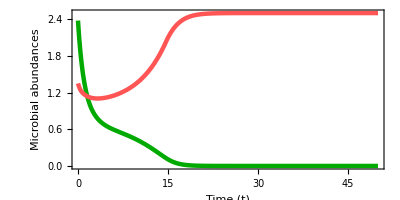

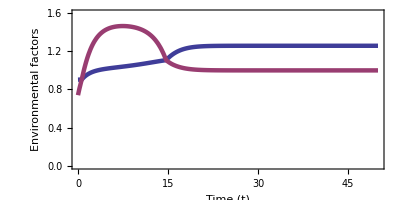

```mathematica
(*trajectory that ends up at the dysbiosis state (red in previous figure)*)
(*Plotting how the abundance of the Mutualist and Pathogen vary through time*)
ass2ab=Quiet[PlotTrajAbun[condini2[[1]],condini2[[2]],50,Thickness[thick2]][[1]]]
(*Plotting how the concentrations of carbon and electron acceptor vary through time*)
ass2env=Quiet[PlotTrajAbun[condini2[[1]],condini2[[2]],50,Thickness[thick2]][[2]]]

(*Exporting the figures*)
Export[StringJoin["figures/fig2d.png"],ass2ab,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig2d.pdf"],ass2ab,"PDF"];
Export[StringJoin["figures/fig2e.png"],ass2env,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig2e.pdf"],ass2env,"PDF"];
```

```mathematica
(*panel b*)
(*Dummy test function to draw the small inset*)
test2[{Sv0_?NumericQ,Pv0_?NumericQ},rcrit_]:=Sv0/Pv0>rcrit;

rcrit=1;
inset=Show[StreamPlot[{Sv,Pv},{Sv,0,Sx},{Pv,0,Px},PlotRange->{{0,Sx},{0,Px}},FrameTicks->None,StreamPoints->15,StreamStyle->{Thickness[2*thick1b],Arrowheads[10*thick1b]},StreamColorFunction->Function[{Sv,Pv},If[test2[{Sv,Pv},rcrit],Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,StreamScale->.2,FrameStyle->Thickness[2.5*thick1b]],Plot[x,{x,0,Sx},PlotRange->{{0,Sx},{0,Px}},PlotStyle->{Gray,Thickness[3*thick1b]}],Plot[x/2.17,{x,1,Sx},PlotRange->{{0,Sx},{0,Px}},PlotStyle->{colS,Thickness[3*thick1b]}],
Plot[x*2.17,{x,.4,Sx},PlotRange->{{0,Sx},{0,Px}},PlotStyle->{colP,Thickness[3*thick1b]}],ImageSize->100,Background->White]
```

-Graphics-

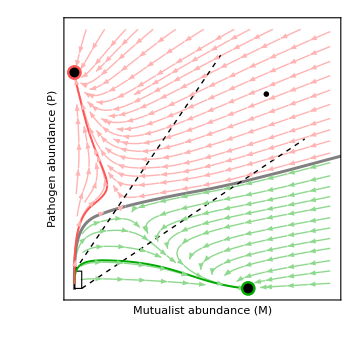

```mathematica
(*New initial conditions*)
condini1={0.0001,.05};
condini2={0.000003,.05};

(*Graphical directives*)
yy=.2;
xx=.1;
fig3b=Show[fig2b,Graphics[{EdgeForm[Directive[Thick,Dashing[.007],Black]],FaceForm[],Rectangle[{0,yy},{xx,0}]}],
Graphics[{Thick,Dashing[.01],Black,Line[{{0,yy},{2,2.7}}]}],
Graphics[{Thick,Dashing[.01],Black,Line[{{xx,0},{3.15,1.73}}]}],
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],10^3,{colP,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]];

(*Drawing the final panel a with the inset*)
fig3=Show[fig3b,Epilog->Inset[inset,{.75*Sx,.75*Px}]]

(*Exporting the figure in PNG and PDF*)
Export[StringJoin["figures/fig3a.png"],fig3,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig3a.pdf"],fig3,"PDF"];
```

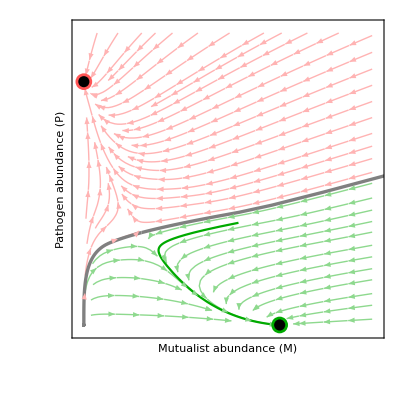

```mathematica
(*panel c*)
(*new initial condition*)
condini1={eqlist[[3,1]]-.5,1.05};

(*drawing panel c*)
fig3b=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]]

(*Exporting the figure in PNG and PDF*)
Export[StringJoin["figures/fig3b.png"],fig3b,"PNG",ImageResolution->200];
Export[StringJoin["figures/fig3b.pdf"],fig3b,"PDF"];
```

## Supplementary Figure 1

### First panel

```mathematica
(*Selecting the supply point for Figure 2; note that this is "supply point A" from Figure 3*)
k=1;
O2in=O2l[[k]];
Cin=Cl[[2]];

(*Displaying where the supply point is located in the niche space*)
s={Cin,O2in};
Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Graphics[ {PointSize[0.02],Point[{s[[1]],s[[2]]}]}]]

(*Setting the dynamical equations for the Quasi Steady State Approximation.
The function "eq" uses the EcoSim function from the EcoEvo package to simulate numerically the equilibriation of O2 and C, leading the QSSA values of O2 and Cb as functions of S and P*)
ClearCache[gS,gP,eq,limP,dgS,dgP];
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2in,Cb->Cin},10^6,Fixed->{S->Sv,P->Pv}]];
gS[Sv_?NumericQ,Pv_?NumericQ]:=gS[Sv,Pv]=(μS-mS/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
gP[Sv_?NumericQ,Pv_?NumericQ]:=gP[Sv,Pv]=(μP-mP/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
limP[Sv_?NumericQ,Pv_?NumericQ]:=limP[Sv,Pv]=(αCP*Cb[t]-αOP*O2[t]/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgS[Sv_?NumericQ,Pv_?NumericQ]:=dgS[Sv,Pv]=(Sv*(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgP[Sv_?NumericQ,Pv_?NumericQ]:=dgP[Sv,Pv]=(Pv*(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])

(*Solving for the different equilibrium points for this supply points*)
eqlist=Join[{{0,0}},If[Min[Bcx[Cin,O2in]]<0,{},{Bcx[Cin,O2in]}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,1;;2]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,1;;2]]]]
(*Checking stability of the different equilibrium points for this supply points*)
stablist=Join[If[(Min[μPx,αCP*Cin,αOP*O2in]-mP<0)&&(Min[μSx,αCS*Cin]-βS*O2in-mS<0),1,{0}],If[Min[Bcx[Cin,O2in]]<0,{},{0}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,3]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,3]]]]

(*Getting the coordinates of the Pathogen equilibrium. Used below for the test function*)
ptH=eqlist[[4]];
```

-Graphics-

{{0,0},{0.700483,0.949275},{2.37722,0},{0,2.5}}

{0,0,1,1}

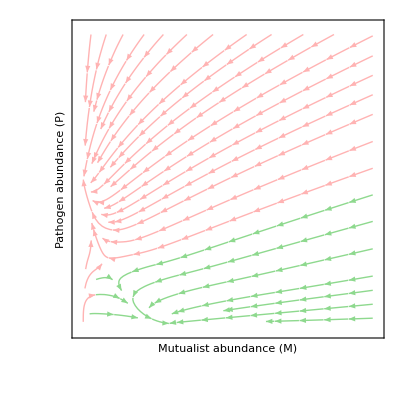

```mathematica
(*Alternative version of this test function to avoid a bug*)
test4[{Sv0_?NumericQ,Pv0_?NumericQ},ptH_]:=Module[{x,y,t,res},res=NDSolveValue[{S'[t]==dgS[S[t],P[t]],P'[t]==dgP[S[t],P[t]],S[0]==Sv0,P[0]==Pv0},{S,P},{t,0,1000}];
Norm[ptH-Through[res[100]]]>.01]
(*test4[{Sv0_?NumericQ,Pv0_?NumericQ},ptH_]:=Module[{x,y,t,res},1;True]*)

(*Resetting the graphical window for the streamplot in the phase plane*)
Sx=8;
Px=5;

(*Actualize the label to include the supply point on top*)
labl2={Row[{Style["Mutualist abundance ",FontSize->ftszlbl],Style[Row[{"(","M",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Pathogen abundance ",FontSize->ftszlbl],Style[Row[{"(","P",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Supply point ",FontSize->ftszlbl],Style[Row[{labpan[[k]]}] ,FontSize->ftszlbl,FontFamily->"Times"]}]};

(*plots the streamplot of the 2D dynamical system*)
stream=StreamPlot[{dgS[Sv,Pv],dgP[Sv,Pv]},{Sv,0,Sx},{Pv,0,Px},StreamColorFunction->Function[{Sv,Pv},If[test4[{Sv,Pv},ptH],Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,FrameTicks->False,FrameLabel -> labl2]
```

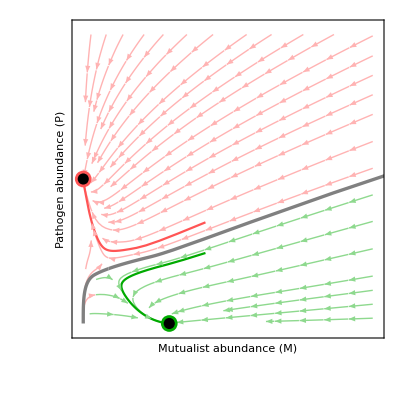

```mathematica
(*Draws the isoclines of the 2D dynamical system (not represented) *)
iso=ContourPlot[{dgS[Sv,Pv]==0,dgP[Sv,Pv]==0(*limP[Sv,Pv]==0,*)},{Sv,0,Sx},{Pv,0,Px},MaxRecursion->5,ContourStyle->{{colS,Thickness[thick2]},{colP,Thickness[thick2]},{colS,Thickness[thick2]},{colP,Thickness[thick2]}},AspectRatio->AR];

(*adds the separatrix between the basin of attraction*)
fig2b=Show[stream,PlotBassin[Cin,O2in,100,-.01],PlotBassin[Cin,O2in,20,.01]];

(*initial conditions for the two trajectories that have been singled out*)
condini1={eqlist[[3,1]]+1,1.22};
condini2={eqlist[[3,1]]+1,1.75};

(*adds the two trajectories; this is the final figure*)
fig2c=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],10^3,{colP,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]]

(*Export the figure in PNG and PDF*)
Export[StringJoin["figures/figSI1.png"],fig2c,"PNG",ImageResolution->200];
Export[StringJoin["figures/figSI1.pdf"],fig2c,"PDF"];
```

### Second panel

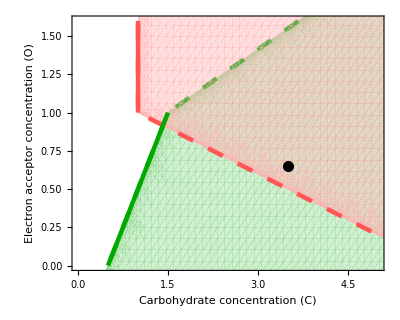

{{0,0},{0.0700483,1.89493},{3.7421,0},{0,2.5},{0,1.75}}

{0,0,1,1,0}

```mathematica
(*Selecting the supply point for Suppl. Figure 1; note that this is "supply point B" from Figure 3*)
k=2;
O2in=O2l[[k]];
Cin=Cl[[2]];
s={Cin,O2in};

(*Displaying where the supply point is located in the niche space*)
Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Graphics[ {PointSize[0.02],Point[{s[[1]],s[[2]]}]}]]

(*Setting the dynamical equations for the Quasi Steady State Approximation and the QSSA growth rates*)
ClearCache[gS,gP,eq,limP,dgS,dgP];
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2in,Cb->Cin},10^6,Fixed->{S->Sv,P->Pv}]];
gS[Sv_?NumericQ,Pv_?NumericQ]:=gS[Sv,Pv]=(μS-mS/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
gP[Sv_?NumericQ,Pv_?NumericQ]:=gP[Sv,Pv]=(μP-mP/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
limP[Sv_?NumericQ,Pv_?NumericQ]:=limP[Sv,Pv]=(αCP*Cb[t]-αOP*O2[t]/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgS[Sv_?NumericQ,Pv_?NumericQ]:=dgS[Sv,Pv]=(Sv*(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgP[Sv_?NumericQ,Pv_?NumericQ]:=dgP[Sv,Pv]=(Pv*(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])

(*Solving for the different equilibrium points for this supply points*)
eqlist=Join[{{0,0}},If[Min[Bcx[Cin,O2in]]<0,{},{Bcx[Cin,O2in]}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,1;;2]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,1;;2]]]]
(*Checking stability of the different equilibrium points for this supply points*)
stablist=Join[If[(Min[μPx,αCP*Cin,αOP*O2in]-mP<0)&&(Min[μSx,αCS*Cin]-βS*O2in-mS<0),1,{0}],If[Min[Bcx[Cin,O2in]]<0,{},{0}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,3]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,3]]]]

(*Getting the coordinates of the Pathogen equilibrium. Used below for the test function*)
ptH=eqlist[[4]];
```

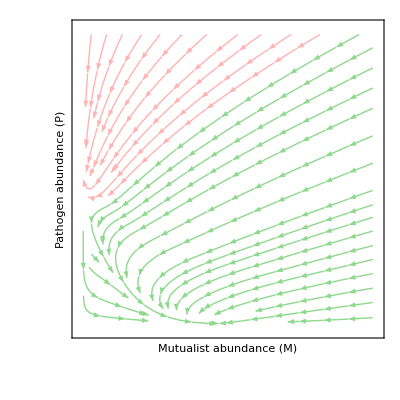

```mathematica
(*Actualize the label to include the supply point on top*)
labl2={Row[{Style["Mutualist abundance ",FontSize->ftszlbl],Style[Row[{"(","M",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Pathogen abundance ",FontSize->ftszlbl],Style[Row[{"(","P",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Supply point ",FontSize->ftszlbl],Style[Row[{labpan[[k]]}] ,FontSize->ftszlbl,FontFamily->"Times"]}]};

(*plots the streamplot of the 2D dynamical system*)
stream=StreamPlot[{dgS[Sv,Pv],dgP[Sv,Pv]},{Sv,0,Sx},{Pv,0,Px},StreamColorFunction->Function[{Sv,Pv},If[test4[{Sv,Pv},ptH],Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,FrameTicks->False,FrameLabel -> labl2]
```

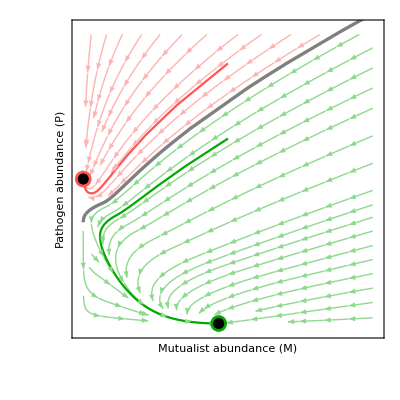

```mathematica
(*Draws the isoclines of the 2D dynamical system (not represented) *)
iso=ContourPlot[{dgS[Sv,Pv]==0,dgP[Sv,Pv]==0(*limP[Sv,Pv]==0,*)},{Sv,0,Sx},{Pv,0,Px},MaxRecursion->5,ContourStyle->{{colS,Thickness[thick2]},{colP,Thickness[thick2]},{colS,Thickness[thick2]},{colP,Thickness[thick2]}},AspectRatio->AR];

(*adds the separatrix between the basin of attraction*)
fig2b=Show[stream,PlotBassin[Cin,O2in,100,-.01],PlotBassin[Cin,O2in,60,.01]];


(*initial conditions for the two trajectories that have been singled out*)
condini1={4,3.2};
condini2={4,4.5};

(*adds the two trajectories; this is the final figure*)
fig2c=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],10^3,{colP,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]]

(*Export the figure in PNG and PDF*)
Export[StringJoin["figures/figSI2.png"],fig2c,"PNG",ImageResolution->200];
Export[StringJoin["figures/figSI2.pdf"],fig2c,"PDF"];
```

### Third panel

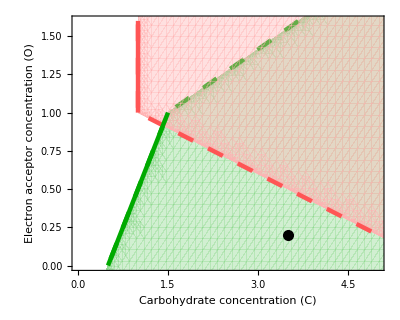

{{0,0},{5.28456,0}}

{0,1}

```mathematica
(*Selecting the supply point for Suppl. Figure 1; note that this is "supply point C" from Figure 3*)
k=3;
O2in=O2l[[k]];
Cin=Cl[[2]];
s={Cin,O2in};

(*Displaying where the supply point is located in the niche space*)
Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Graphics[ {PointSize[0.02],Point[{s[[1]],s[[2]]}]}]]

(*Setting the dynamical equations for the Quasi Steady State Approximation and the QSSA growth rates*)
ClearCache[gS,gP,eq,limP,dgS,dgP];
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2in,Cb->Cin},10^6,Fixed->{S->Sv,P->Pv}]];
gS[Sv_?NumericQ,Pv_?NumericQ]:=gS[Sv,Pv]=(μS-mS/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
gP[Sv_?NumericQ,Pv_?NumericQ]:=gP[Sv,Pv]=(μP-mP/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
limP[Sv_?NumericQ,Pv_?NumericQ]:=limP[Sv,Pv]=(αCP*Cb[t]-αOP*O2[t]/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgS[Sv_?NumericQ,Pv_?NumericQ]:=dgS[Sv,Pv]=(Sv*(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgP[Sv_?NumericQ,Pv_?NumericQ]:=dgP[Sv,Pv]=(Pv*(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])

(*Solving for the different equilibrium points for this supply points*)
eqlist=Join[{{0,0}},If[Min[Bcx[Cin,O2in]]<0,{},{Bcx[Cin,O2in]}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,1;;2]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,1;;2]]]]
(*Checking stability of the different equilibrium points for this supply points*)
stablist=Join[If[(Min[μPx,αCP*Cin,αOP*O2in]-mP<0)&&(Min[μSx,αCS*Cin]-βS*O2in-mS<0),1,{0}],If[Min[Bcx[Cin,O2in]]<0,{},{0}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,3]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,3]]]]
```

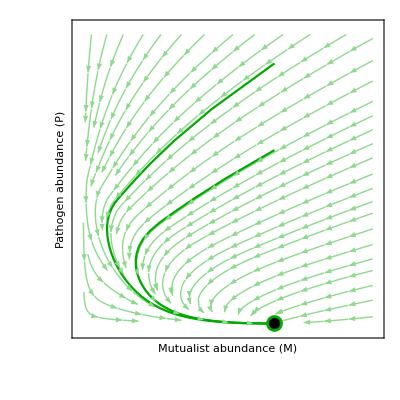

```mathematica
(*dummy test function that always returns true, as we know that there is no pathogen equilibrium in this situation (speeds up the simulation)*)
test3[{Sv0_?NumericQ,Pv0_?NumericQ},ptH_]:=Module[{x,y,t,res},1;True]

(*Actualize the label to include the supply point on top*)
labl2={Row[{Style["Mutualist abundance ",FontSize->ftszlbl],Style[Row[{"(","M",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Pathogen abundance ",FontSize->ftszlbl],Style[Row[{"(","P",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Supply point ",FontSize->ftszlbl],Style[Row[{labpan[[k]]}] ,FontSize->ftszlbl,FontFamily->"Times"]}]};

(*plots the streamplot of the 2D dynamical system*)
stream=StreamPlot[{dgS[Sv,Pv],dgP[Sv,Pv]},{Sv,0,Sx},{Pv,0,Px},StreamColorFunction->Function[{Sv,Pv},If[test3[{Sv,Pv},ptH],Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,FrameTicks->False,FrameLabel -> labl2];

(*Draws the isoclines of the 2D dynamical system (not represented) *)
iso=ContourPlot[{dgS[Sv,Pv]==0,dgP[Sv,Pv]==0(*limP[Sv,Pv]==0,*)},{Sv,0,Sx},{Pv,0,Px},MaxRecursion->5,ContourStyle->{{colS,Thickness[thick2]},{colP,Thickness[thick2]},{colS,Thickness[thick2]},{colP,Thickness[thick2]}},FrameLabel -> labl2,AspectRatio->AR];

(*adds the separatrix between the basin of attraction*)
fig2b=Show[stream,PlotBassin[Cin,O2in,100,-.01],PlotBassin[Cin,O2in,35.75,.01]];

(*initial conditions for the two trajectories that have been singled out*)
condini1={eqlist[[2,1]],3};
condini2={eqlist[[2,1]],4.5};

(*adds the two trajectories; this is the final figure*)
fig2c=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],10^3,{colS,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{2}}]]

(*Export the figure in PNG and PDF*)
Export[StringJoin["figures/figSI3.png"],fig2c,"PNG",ImageResolution->200];
Export[StringJoin["figures/figSI3.pdf"],fig2c,"PDF"];
```

### Fourth panel

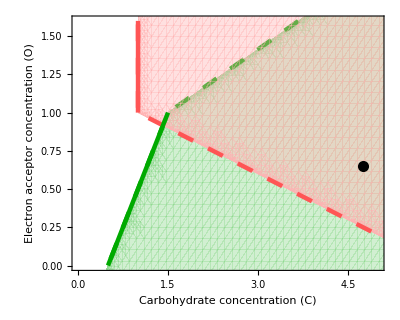

{{0,0},{0.42029,2.61957},{6.1031,0},{0,3.75},{0,1.75}}

{0,0,1,1,0}

```mathematica
(*Selecting the supply point for Suppl. Figure 1; note that this is "supply point E" from Figure 3*)
k=3;
O2in=O2l[[2]];
Cin=Cl[[k]];

(*Displaying where the supply point is located in the niche space*)
s={Cin,O2in};
Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Graphics[ {PointSize[0.02],Point[{s[[1]],s[[2]]}]}]]

(*Setting the dynamical equations for the Quasi Steady State Approximation and the QSSA growth rates*)
ClearCache[gS,gP,eq,limP,dgS,dgP];
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2in,Cb->Cin},10^6,Fixed->{S->Sv,P->Pv}]];
gS[Sv_?NumericQ,Pv_?NumericQ]:=gS[Sv,Pv]=(μS-mS/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
gP[Sv_?NumericQ,Pv_?NumericQ]:=gP[Sv,Pv]=(μP-mP/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
limP[Sv_?NumericQ,Pv_?NumericQ]:=limP[Sv,Pv]=(αCP*Cb[t]-αOP*O2[t]/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgS[Sv_?NumericQ,Pv_?NumericQ]:=dgS[Sv,Pv]=(Sv*(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgP[Sv_?NumericQ,Pv_?NumericQ]:=dgP[Sv,Pv]=(Pv*(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])

(*Solving for the different equilibrium points for this supply points*)
eqlist=Join[{{0,0}},If[Min[Bcx[Cin,O2in]]<0,{},{Bcx[Cin,O2in]}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,1;;2]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,1;;2]]]]
(*Checking stability of the different equilibrium points for this supply points*)
stablist=Join[If[(Min[μPx,αCP*Cin,αOP*O2in]-mP<0)&&(Min[μSx,αCS*Cin]-βS*O2in-mS<0),1,{0}],If[Min[Bcx[Cin,O2in]]<0,{},{0}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,3]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,3]]]]

(*Getting the coordinates of the Pathogen equilibrium. Used below for the test function*)
ptH=eqlist[[4]];
```

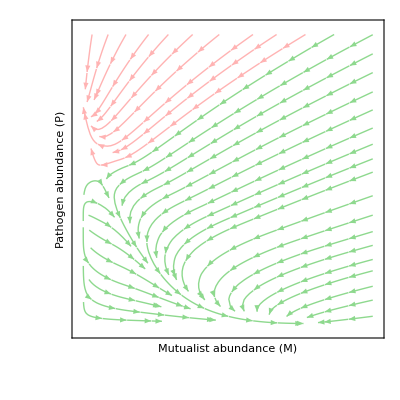

```mathematica
(*Actualize the label to include the supply point on top*)
labl2={Row[{Style["Mutualist abundance ",FontSize->ftszlbl],Style[Row[{"(","M",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Pathogen abundance ",FontSize->ftszlbl],Style[Row[{"(","P",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Supply point ",FontSize->ftszlbl],Style[Row[{labpan2[[k]]}] ,FontSize->ftszlbl,FontFamily->"Times"]}]};

(*plots the streamplot of the 2D dynamical system*)
stream=StreamPlot[{dgS[Sv,Pv],dgP[Sv,Pv]},{Sv,0,Sx},{Pv,0,Px},StreamColorFunction->Function[{Sv,Pv},If[test4[{Sv,Pv},ptH]||(Pv<2.6),Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,FrameTicks->False,FrameLabel -> labl2]
```

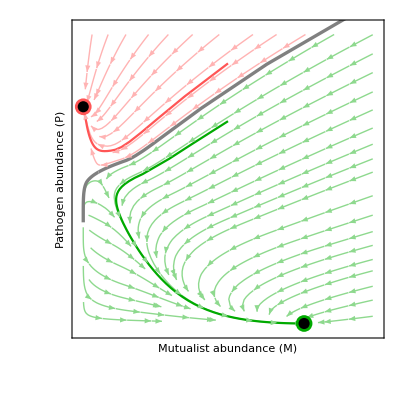

```mathematica
(*Draws the isoclines of the 2D dynamical system (not represented) *)
iso=ContourPlot[{dgS[Sv,Pv]==0,dgP[Sv,Pv]==0(*limP[Sv,Pv]==0,*)},{Sv,0,Sx},{Pv,0,Px},MaxRecursion->5,ContourStyle->{{colS,Thickness[thick2]},{colP,Thickness[thick2]},{colS,Thickness[thick2]},{colP,Thickness[thick2]}},AspectRatio->AR];
(*adds the separatrix between the basin of attraction*)
fig2b=Show[stream,PlotBassin[Cin,O2in,100,-.01],PlotBassin[Cin,O2in,20,.01]];

(*initial conditions for the two trajectories that have been singled out*)
condini1={4,3.5};
condini2={4,4.5};

(*adds the two trajectories; this is the final figure*)
fig2c=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],10^3,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],10^3,{colP,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{3,4}}]]

(*Export the figure in PNG and PDF*)
Export[StringJoin["figures/figSI4.png"],fig2c,"PNG",ImageResolution->200];
Export[StringJoin["figures/figSI4.pdf"],fig2c,"PDF"];
```

### Fifth panel

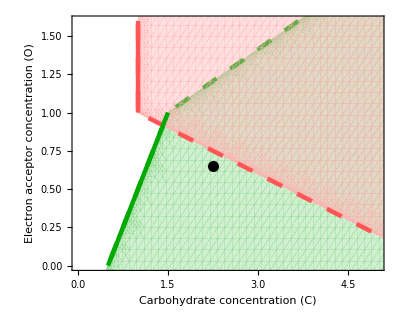

{{0,0},{1.55106,0}}

{0,1}

```mathematica
(*Selecting the supply point for Suppl. Figure 1; note that this is "supply point D" from Figure 3*)
k=1;
O2in=O2l[[2]];
Cin=Cl[[k]];

(*Displaying where the supply point is located in the niche space*)
s={Cin,O2in};
Show[PlotPersist2[spSu,spP,labl],PlotPersist[spP,labl],PlotZNGI[spP,thick2,labl],PlotZNGI[spSu,thick2,labl],Graphics[ {PointSize[0.02],Point[{s[[1]],s[[2]]}]}]]

(*Setting the dynamical equations for the Quasi Steady State Approximation and the QSSA growth rates*)
ClearCache[gS,gP,eq,limP,dgS,dgP];
eq[Sv_?NumericQ,Pv_?NumericQ]:=eq[Sv,Pv]=FinalSlice[EcoSim[{O2->O2in,Cb->Cin},10^6,Fixed->{S->Sv,P->Pv}]];
gS[Sv_?NumericQ,Pv_?NumericQ]:=gS[Sv,Pv]=(μS-mS/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
gP[Sv_?NumericQ,Pv_?NumericQ]:=gP[Sv,Pv]=(μP-mP/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
limP[Sv_?NumericQ,Pv_?NumericQ]:=limP[Sv,Pv]=(αCP*Cb[t]-αOP*O2[t]/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgS[Sv_?NumericQ,Pv_?NumericQ]:=dgS[Sv,Pv]=(Sv*(μS-mS)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])
dgP[Sv_?NumericQ,Pv_?NumericQ]:=dgP[Sv,Pv]=(Pv*(μP-mP)/.{O2[t]->O2,Cb[t]->Cb}/.eq[Sv,Pv])

(*Solving for the different equilibrium points for this supply points*)
eqlist=Join[{{0,0}},If[Min[Bcx[Cin,O2in]]<0,{},{Bcx[Cin,O2in]}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,1;;2]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,1;;2]]]]
(*Checking stability of the different equilibrium points for this supply points*)
stablist=Join[If[(Min[μPx,αCP*Cin,αOP*O2in]-mP<0)&&(Min[μSx,αCS*Cin]-βS*O2in-mS<0),1,{0}],If[Min[Bcx[Cin,O2in]]<0,{},{0}],If[GivesolS[Cin,O2in]=={},{},GivesolS[Cin,O2in][[1;;-1,3]]],If[GivesolP[Cin,O2in]=={},{},GivesolP[Cin,O2in][[1;;-1,3]]]]
```

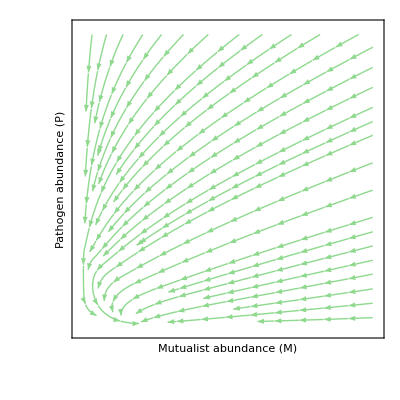

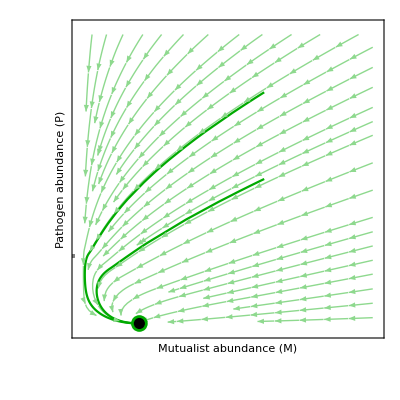

```mathematica
(*Actualize the label to include the supply point on top*)
labl2={Row[{Style["Mutualist abundance ",FontSize->ftszlbl],Style[Row[{"(","M",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Pathogen abundance ",FontSize->ftszlbl],Style[Row[{"(","P",")"}] ,FontSlant->Italic,FontSize->ftszlbl,FontFamily->"Times"]}],Row[{Style["Supply point ",FontSize->ftszlbl],Style[Row[{labpan2[[k]]}] ,FontSize->ftszlbl,FontFamily->"Times"]}]};

(*plots the streamplot of the 2D dynamical system*)
stream=StreamPlot[{dgS[Sv,Pv],dgP[Sv,Pv]},{Sv,0,Sx},{Pv,0,Px},StreamColorFunction->Function[{Sv,Pv},If[test3[{Sv,Pv},ptH],Lighter[Lighter[colS]],Lighter[Lighter[colP]]]],StreamColorFunctionScaling->False,FrameTicks->False,FrameLabel -> labl2]

(*Draws the isoclines of the 2D dynamical system (not represented) *)
iso=ContourPlot[{dgS[Sv,Pv]==0,dgP[Sv,Pv]==0(*limP[Sv,Pv]==0,*)},{Sv,0,Sx},{Pv,0,Px},MaxRecursion->5,ContourStyle->{{colS,Thickness[thick2]},{colP,Thickness[thick2]},{colS,Thickness[thick2]},{colP,Thickness[thick2]}},AspectRatio->AR];
(*adds the separatrix between the basin of attraction*)
fig2b=Show[stream,PlotBassin[Cin,O2in,100,-.01],PlotBassin[Cin,O2in,20,.01]];

(*initial conditions for the two trajectories that have been singled out*)
condini1={5,4};
condini2={5,2.5};

(*adds the two trajectories; this is the final figure*)
fig2c=Show[fig2b,
PlotTraj[condini1[[1]],condini1[[2]],100,{colS,Thickness[thick1]}],
PlotTraj[condini2[[1]],condini2[[2]],100,{colS,Thickness[thick1]}],
Table[PtPoint[eqlist[[k]],stablist[[k]]],{k,{2}}]]

(*Export the figure in PNG and PDF*)
Export[StringJoin["figures/figSI5.png"],fig2c,"PNG",ImageResolution->200];
Export[StringJoin["figures/figSI5.pdf"],fig2c,"PDF"];
```